# Exploring Graph Programming

Graph Programming Reference

## Manipulating Vertex and Edge Properties

## Property

### List of Vertex Properties

VertexStyle

VertexLabels

VertexSize

VertexShape

VertexShapeFunction

VertexWeight

Custom

### Vertex Property Examples

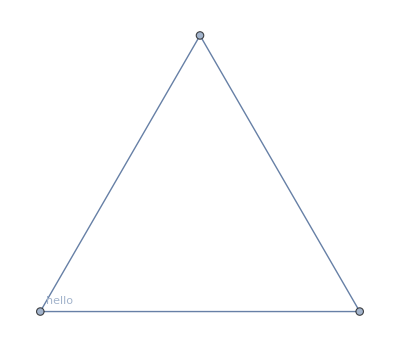

```mathematica
Graph[{Property[1,VertexLabels-> "hello"],2,3},{1<->2,2<->3,3<->1}]
```

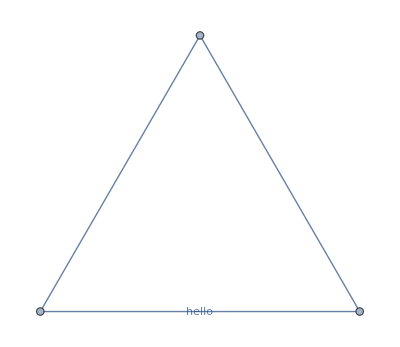

```mathematica
Graph[{Property[1<->2,EdgeLabels->"hello"],2<->3,3<->1}]
```

```mathematica
Graph[{Labeled[1,"hello"],2,3},{1<->2,2<->3,3<->1}]
```

-Graphics-

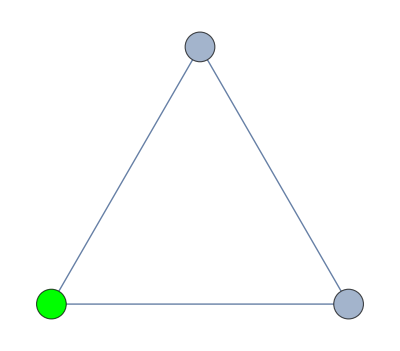

```mathematica
Graph[{Style[1,Green],2,3},{1<->2,2<->3,3<->1},VertexSize->Small]
```

### Custom Vertex Properties

```mathematica
Graph[{Property[1,"Material"->"Wood"],2,3},{1<->2,2<->3,3<->1}]
```

-Graphics-

```mathematica
PropertyValue[{%1758,1},"Material"]
```

Wood

### List of Edge Properties

EdgeStyle

EdgeLabels

EdgeShapeFunction

EdgeWeight

Custom

### Edge Property Examples

```mathematica
GraphElementData["Edge"]
```

{Arrow,BoxLine,CarvedArcArrow,CarvedArrow,DashedLine,DiamondLine,DotLine,DottedLine,FilledArcArrow,FilledArrow,HalfFilledArrow,HalfFilledDoubleArrow,HalfUnfilledArrow,HalfUnfilledDoubleArrow,Line,ShortCarvedArcArrow,ShortCarvedArrow,ShortFilledArcArrow,ShortFilledArrow,ShortUnfilledArcArrow,ShortUnfilledArrow,UnfilledArcArrow,UnfilledArrow}

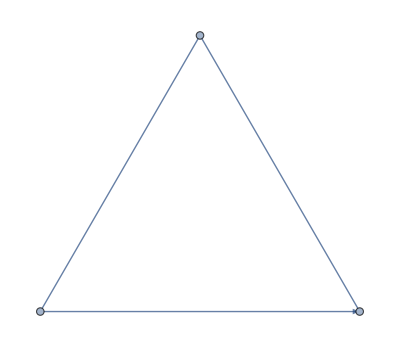
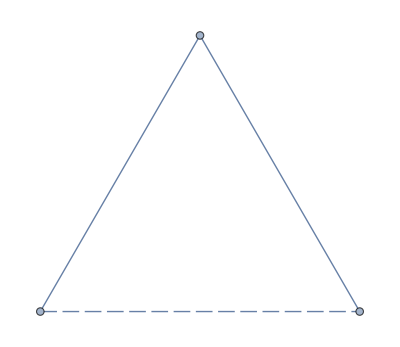
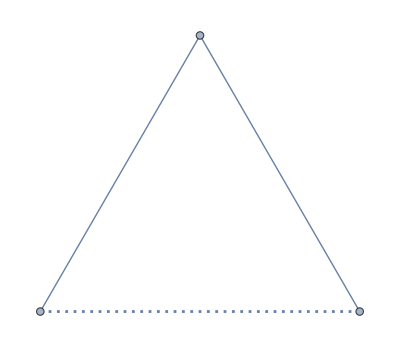
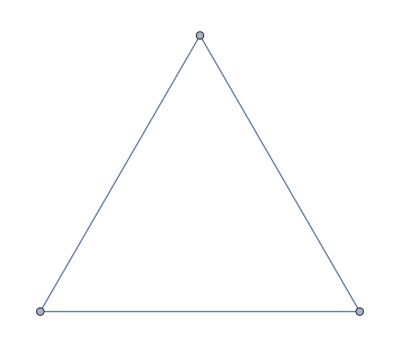
-Graphics-Arrow | -Graphics-BoxLine | -Graphics-CarvedArcArrow | -Graphics-CarvedArrow | -Graphics-DashedLine
-Graphics-DiamondLine | -Graphics-DotLine | -Graphics-DottedLine | -Graphics-FilledArcArrow | -Graphics-FilledArrow
-Graphics-HalfFilledArrow | -Graphics-HalfFilledDoubleArrow | -Graphics-HalfUnfilledArrow | -Graphics-HalfUnfilledDoubleArrow | -Graphics-Line
-Graphics-ShortCarvedArcArrow | -Graphics-ShortCarvedArrow | -Graphics-ShortFilledArcArrow | -Graphics-ShortFilledArrow | -Graphics-ShortUnfilledArcArrow
-Graphics-ShortUnfilledArrow | -Graphics-UnfilledArcArrow | -Graphics-UnfilledArrow |  |

```mathematica
Multicolumn[Labeled[Graph[{Property[1<->2,EdgeShapeFunction->#],2<->3,3<->1}], #]&/@GraphElementData["Edge"],Appearance -> "Horizontal", Frame -> All]
```

### Custom Edge Properties

```mathematica
Graph[{Property[1,"Material"->"Wood"],2,3},{1<->2,2<->3,3<->1}]
```

-Graphics-

```mathematica
PropertyValue[{%1758,1},"Material"]
```

Wood

### Set, Unset, Get Properties

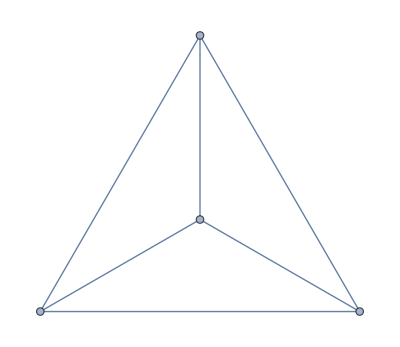

```mathematica
g=CompleteGraph[4]
```

#### Set | Nondestructive

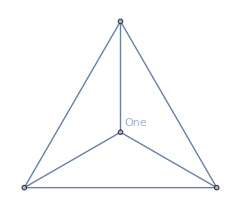

```mathematica
SetProperty[{g, 1}, VertexLabels -> "One"]
```

```mathematica
g
```

-Graphics-

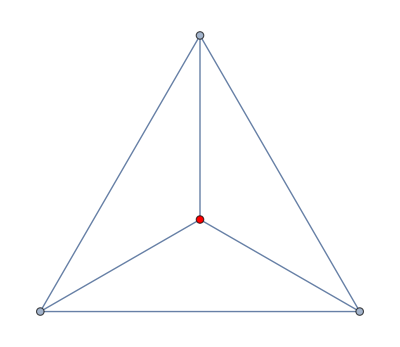

```mathematica
SetProperty[{g, 1}, VertexStyle -> Red]
```

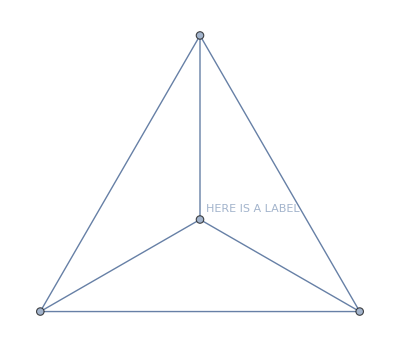
{-Graphics-,-Graphics-}

```mathematica
{g,SetProperty[{g, 1}, VertexLabels -> "HERE IS A LABEL"]}
```

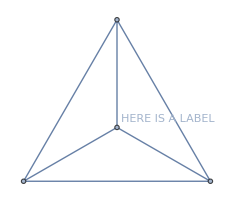

```mathematica
gra =SetProperty[{g, 1}, VertexLabels -> "HERE IS A LABEL"]
```

```mathematica
{gra,RemoveProperty[{gra, 1}, VertexLabels]}
```

{-Graphics-,-Graphics-}

#### Set / Unset | Destructive

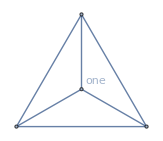

```mathematica
gr = CompleteGraph[4,VertexLabels->{1->"one"}]
```

Change the Property Value

```mathematica
PropertyValue[{gr, 1}, VertexLabels] = Orange;
```

```mathematica
gr
```

-Graphics-

Unset / Remove the property

```mathematica
PropertyValue[{gr, 1}, VertexLabels] =.;
```

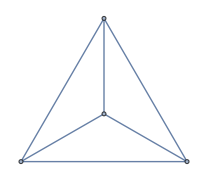

```mathematica
gr
```

### Vertex Shape Functions

```mathematica
GraphElementData["VertexShapeFunction"]
```

{Capsule,Circle,ConcaveDiamond,ConcaveHexagon,ConcavePentagon,ConcaveSquare,ConcaveTriangle,Diamond,DownTrapezoid,FiveDown,Hexagon,Octagon,Parallelogram,Pentagon,Point,Rectangle,RoundedDiamond,RoundedDownTrapezoid,RoundedFiveDown,RoundedHexagon,RoundedParallelogram,RoundedPentagon,RoundedRectangle,RoundedSquare,RoundedTriangle,RoundedUpTrapezoid,Square,Star,Triangle,UpTrapezoid}

### Vertex Replace

```mathematica
VertexReplace[-Graphics-,Table[i->Subscript[v, i],{i,4}]]
```

-Graphics-

## Scan Based Algorithms

```mathematica
BreadthFirstScan[-Graphics-,1,{"PrevisitVertex"->(Echo[#, "Visiting "]&)}];
```

Visiting  1

Visiting  2

Visiting  3

Visiting  4

Visiting  5

Visiting  6

Visiting  7

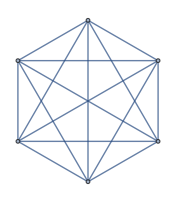

```mathematica
cg =CompleteGraph[6]
```

Perform a bfs of the graph cg starting at vertex 1 and evaluates Echo[#, “Visiting ”]&

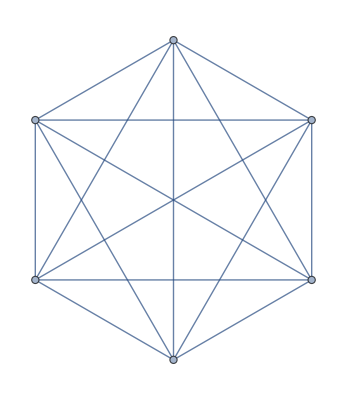
```mathematica
BreadthFirstScan[-Graphics-,1,{"PrevisitVertex"->(Echo[#, "Visiting "]&)}];
```

Visiting  1

Visiting  2

Visiting  3

Visiting  4

Visiting  5

Visiting  6

```mathematica
DepthFirstScan[-Graphics-,1,{"PrevisitVertex"->(Echo[#, "Visiting "]&)}];
```

Visiting  1

Visiting  2

Visiting  3

Visiting  4

Visiting  5

Visiting  6

## Extracting Graph Information

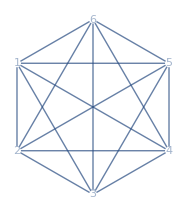

```mathematica
grap = CompleteGraph[6, VertexShapeFunction-> "Name"]
```

```mathematica
VertexList[grap]
```

{1,2,3,4,5,6}

```mathematica
EdgeList[grap]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6}

```mathematica
VertexIndex[grap,3 ]
```

3

```mathematica
EdgeIndex[grap,3<->4 ]
```

10

```mathematica
EdgeRules[grap]
```

{1→2,1→3,1→4,1→5,1→6,2→3,2→4,2→5,2→6,3→4,3→5,3→6,4→5,4→6,5→6}

```mathematica
IncidenceList[grap,1]
```

{1<->2,1<->3,1<->4,1<->5,1<->6}

## Thoughts so far

Current Graph representation is fine

Association needs to be reformed:

From  <| "title" → "value", "passageName" → "passageContent",...|>

To        <| “title” →       <| “passageName” → “passageContent”,...|> |>

Use BFS and DFS to traverse the graph when necessary

Need to think about a story representation that is compatible with a “story explorer” | RelationGraph

Need to think about an “inline” way to write long-form Twine Stories

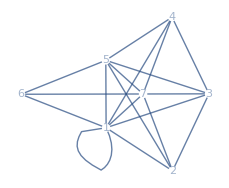

```mathematica
RelationGraph[CoprimeQ, {1,2,3,4,5,6,7}, VertexLabels -> None,VertexShapeFunction->"Name"]
```

```mathematica
RelationGraph[CoprimeQ, {1,2,3,4,5,6,7}, VertexLabels -> None,VertexShapeFunction->"Name"]
```

```mathematica
RelationGraph[# === "Is" ∨# === "Really"∨ # === "Cool"&, {"Here","Is","My","Really","Amazingly","Cool","Graph"}, VertexLabels -> None,VertexShapeFunction->"Name"]
```

-Graphics-

```mathematica
list ={"Here","Is","My","Really","Amazingly","Cool","Graph"};
```

```mathematica
listVal =Thread[List[list ,  RandomReal[1,Length[list] ]]]
```

{{Here,0.324115},{Is,0.443929},{My,0.597837},{Really,0.34977},{Amazingly,0.484745},{Cool,0.984534},{Graph,0.400012}}

```mathematica
#⟦2⟧ &/@listVal
```

{0.324115,0.443929,0.597837,0.34977,0.484745,0.984534,0.400012}

```mathematica
RelationGraph[#⟦2⟧ > .5&, listVal, VertexLabels -> None,VertexShapeFunction->"Name"]
```

-Graphics-